```mathematica
L1:=(-6 r^2 f[r]-3 r^3 f'[r]) NN'[r]+NN[r] (6 r-6 r f[r]-6 r^2 f'[r]-r^3 f''[r])-2 r^3 f[r] NN''[r]
L2:=(-4 f[r]+4 f[r]^2-6 r f'[r]+10 r f[r] f'[r]) NN'[r]+NN[r] (-4 f'[r]+4 f[r] f'[r]+2 r f'[r]^2-2 r f''[r]+2 r f[r] f''[r])+(-4 r f[r]+4 r f[r]^2) NN''[r]
L3:=1/r^3(-1+f[r]) (NN[r] (2+2 f[r]^2+6 r f'[r]+6 r^2 f'[r]^2-3 r^2 f''[r]+f[r] (-4-6 r f'[r]+3 r^2 f''[r]))+3 r (-3 r f'[r] NN'[r]+f[r] ((2+7 r f'[r]) NN'[r]-2 r NN''[r])-2 f[r]^2 (NN'[r]-r NN''[r])))
```

```mathematica
L=Collect[Simplify[(L1/3+(α^2)*L3)],{NN[r],NN'[r],NN''[r]}]
```

(-2 r^2 f[r]-(6 α^2 (-1+f[r]) f[r]^2)/r^2-r^3 f'[r]-(9 α^2 (-1+f[r]) f'[r])/r+(3 α^2 (-1+f[r]) f[r] (2+7 r f'[r]))/r^2) NN'[r]+NN[r] (-1/3 r (-6+6 f[r]+6 r f'[r]+r^2 f''[r])+1/r^3 α^2 (-1+f[r]) (2+2 f[r]^2+6 r f'[r]+6 r^2 f'[r]^2-3 r^2 f''[r]+f[r] (-4-6 r f'[r]+3 r^2 f''[r])))+(-2/3 r^3 f[r]-(6 α^2 (-1+f[r]) f[r])/r+(6 α^2 (-1+f[r]) f[r]^2)/r) NN''[r]

```mathematica
F0'[r_]:=Coefficient[L,NN[r]]
F1[r_]:=Coefficient[L,NN'[r]]
F2[r_]:=Coefficient[L,NN''[r]]
funcion4=Simplify[Integrate[F0'[r],r]-F1[r]+D[F2[r],r]]
```

-((-1+f[r]) (r^4+α^2-2 α^2 f[r]+α^2 f[r]^2))/r^2

```mathematica
f4=f[r]/. Solve[funcion4==μ,f[r],Reals][[1]]
```

Root[-r^4-α^2+r^2 μ+(r^4+3 α^2) #1-3 α^2 #1^2+α^2 #1^3&,1]

```mathematica
q4=ToRadicals[f4]==0
```

1-((2/3)^(1/3) r^4)/((-9 r^2 α^4 μ+√3 √(4 r^12 α^6+27 r^4 α^8 μ^2))^(1/3))+((-9 r^2 α^4 μ+√3 √(4 r^12 α^6+27 r^4 α^8 μ^2))^(1/3))/(2^(1/3) 3^(2/3) α^2)==0

```mathematica
Clear[α,μ]
```

```mathematica
α:=0.03
μ:=1
```

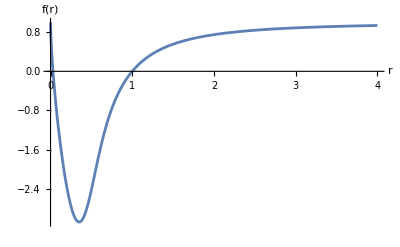

```mathematica
Plot[f4,{r,0,4},AxesLabel->{"r","f(r)"},PlotRange->All]
```

```mathematica
Solve[q4,r]
```